0.3757

1.32

0.589

0.030104

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Ko→0.00449923,λ0→0.345277}

{Ko→0.00449833,λ0→0.345313}

{Ko→0.00449016,λ0→0.345641}

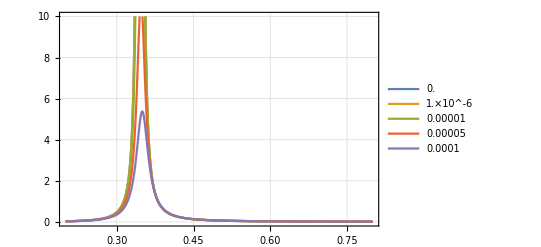

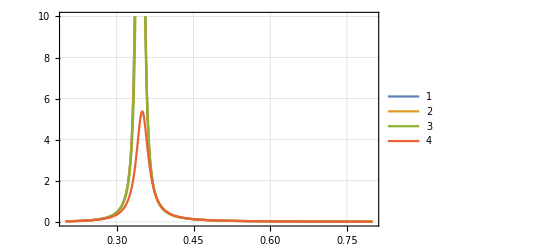

```mathematica
λ1=0.3757
ϰ1=1.32
λ2=0.589
ϰ2=0.030104
xi[lambda_]:=Ko lambda^2/(ϵ+(lambda^2-λ0^2)^2);
sol=Solve[{xi[λ1]==ϰ1,xi[λ2]==ϰ2},{Ko,λ0}];
Simplify[sol /. {ϵ -> 0}][[2]]
Simplify[sol /. {ϵ -> 10^-6}][[2]]
Simplify[sol /. {ϵ -> 10^-5}][[2]]

xi[lambda_, eps_]:=((xi[λ] /. sol[[2]]) /. {ϵ -> eps});
epsTbl=N[{0, 10^-6, 10^-5, 5 10^-5, 10^-4}];
xiTbl=Table[xi[λ, epsTbl[[ii]]],{ii, Length[epsTbl]}];

Plot[xiTbl,{λ,0.2,0.8}, Frame->True, GridLines->Automatic, PlotRange->{0, 10}, PlotLegends->epsTbl]

Plot[{xi[λ, 0], xi[λ, 10^-6], xi[λ, 10^-5], xi[λ, 10^-4]},{λ,0.2,0.8}, Frame->True, GridLines->Automatic, PlotRange->{0, 10}, PlotLegends->Automatic]
```